#### import data

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Conductivity_ZrC/Band_life_broadened/TOTAL"];
filesLINE={"c.lw.10","c.lw.300","c.lw.1000","c.lw.3800"};
(*Exclude the DOS with zero smearing*)
lineWidths=Table[ReadList[filesLINE[[i]],{Number,Number,Number,Number,Number,Number,Number}],{i,1,filesLINE//Length}];
bands=ReadList["clong.bands",{Number,Number,Number,Number,Number,Number,Number}];
```

```mathematica
b=Table[DeleteDuplicates@Transpose[{Transpose[bands][[1]],Transpose[bands][[i+1]]}],{i,1,Length[Transpose[bands]]-1}];
```

```mathematica
lw10=Table[DeleteDuplicates@Transpose[{Transpose[lineWidths[[1]]][[1]],Transpose[lineWidths[[1]]][[i+1]]}],{i,1,Length[Transpose[lineWidths[[1]]]]-1}];
lw300=Table[DeleteDuplicates@Transpose[{Transpose[lineWidths[[1]]][[1]],Transpose[lineWidths[[2]]][[i+1]]}],{i,1,Length[Transpose[lineWidths[[2]]]]-1}];
lw1000=Table[DeleteDuplicates@Transpose[{Transpose[lineWidths[[1]]][[1]],Transpose[lineWidths[[3]]][[i+1]]}],{i,1,Length[Transpose[lineWidths[[3]]]]-1}];
lw3800=Table[DeleteDuplicates@Transpose[{Transpose[lineWidths[[1]]][[1]],Transpose[lineWidths[[4]]][[i+1]]}],{i,1,Length[Transpose[lineWidths[[4]]]]-1}];
```

```mathematica
interb=Table[Interpolation[b[[i]]],{i,1,Length[b]}];
interlw10=Table[Interpolation[lw10[[i]]],{i,1,Length[lw10]}];
interlw300=Table[Interpolation[lw300[[i]]],{i,1,Length[lw300]}];
interlw1000=Table[Interpolation[lw1000[[i]]],{i,1,Length[lw1000]}];
interlw3800=Table[Interpolation[lw3800[[i]]],{i,1,Length[lw3800]}];
```

```mathematica
lw10[[2]][[-1]]
```

{0.81005,5.26731×10^-10}

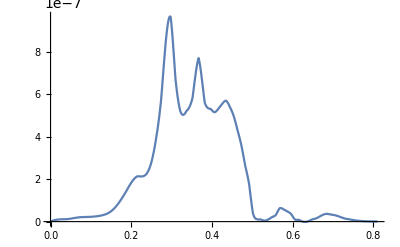

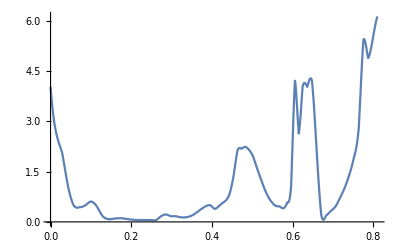

```mathematica
Plot[interlw10[[1]][x],{x,0,0.81}]
Plot[interlw3800[[6]][x],{x,0,0.81}]
```

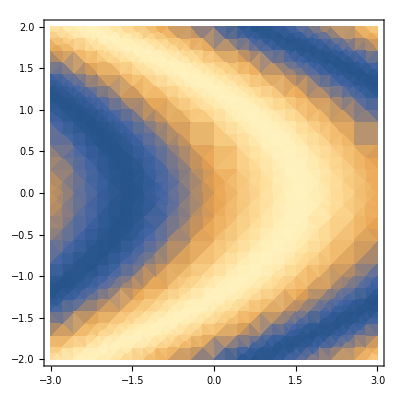

```mathematica
DensityPlot[Sin[x+y^2],{x,-3,3},{y,-2,2},PlotLegends->BarLegend[Automatic,LegendMarkerSize->180,LegendFunction->"Frame",LegendMargins->5,LegendLabel->"z-value"]]
```

## Production plots

```mathematica
With[{height=1,width=1,baseWidth=0.01},Table[(baseWidth+height)*PDF[CauchyDistribution[interb[[i]][x],(baseWidth+width*(interlw3800[[i]][x]))],y],{i,1,6}]];
pltB4=Show[{DensityPlot[Total@%,{x,0,0.81},{y,-0.1,22},PlotRange->All,Frame->True,FrameTicksStyle->20,PlotPoints->100,FrameLabel->{Style["Reciprocal space (Å^-1)",20],Style["Energy (THz)",20]},ColorFunction->GrayLevel,PlotTheme->"Scientific",PlotLabel->Style["3800K",20],PlotLegends->BarLegend[Automatic,Method->{Frame->False,TicksStyle->Directive[FontSize->18,AbsoluteThickness[2]]},LegendMarkerSize->300,LegendLabel->Style["Γ(ω,T)\n(THz)",18]]],Plot[{interb[[1]][x],interb[[2]][x],interb[[3]][x],interb[[4]][x],interb[[5]][x],interb[[6]][x]},{x,0,0.81},PlotStyle->Directive[Orange,Opacity[0.9],Thickness[0.002]],PlotTheme->"Scientific"],
Graphics[{Text[Style["Γ",22,Bold,FontFamily->"Times",Hue[0.13]],{0.02,21}]}],Graphics[{Text[Style["X",22,Bold,FontFamily->"Times",Hue[0.13]],{0.224,21}]}],Graphics[{Text[Style["W",22,Bold,FontFamily->"Times",Hue[0.13]],{0.348,21}]}],Graphics[{Text[Style["K",22,Bold,FontFamily->"Times",Hue[0.13]],{0.419,21}]}],Graphics[{Text[Style["Γ",22,Bold,FontFamily->"Times",Hue[0.13]],{0.644,21}]}],
Graphics[{Text[Style["L",22,Bold,FontFamily->"Times",Hue[0.13]],{0.78,21}]}],Graphics[{Directive[{Thin,Orange,Dashed}],Line[{{0.202,0},{0.202,22}}]}],Graphics[{Directive[{Thin,Orange,Dashed}],Line[{{0.321,0},{0.321,22}}]}],Graphics[{Directive[{Thin,Orange,Dashed}],Line[{{0.397,0},{0.397,22}}]}],Graphics[{Directive[{Thin,Orange,Dashed}],Line[{{0.624,0},{0.624,22}}]}]},ImageSize->400]
```

-Graphics-

#### Lorentzians:;

10K

```mathematica
With[{height=100,width=100,baseWidth=0.01},Table[(baseWidth+height*(interlw10[[i]][x]))*PDF[CauchyDistribution[interb[[i]][x],(baseWidth+width*(interlw10[[i]][x]))],y],{i,1,6}]];
DensityPlot[Total@%,{x,0,0.81},{y,-0.1,22},PlotRange->All,Frame->True,PlotPoints->100,FrameTicks->{{{0,5,10,15,20},None},{{{0,"Γ"},{0.2,"X"},{0.32,"W"},{0.39,"K"},{0.62,"Γ"},{0.83,"L"}},None}}]
```

-Graphics-

```mathematica
With[{height=100,width=100,baseWidth=0.01},Table[(baseWidth+height*(interlw10[[i]][x]))*PDF[CauchyDistribution[interb[[i]][x],(baseWidth+width*(interlw10[[i]][x]))],y],{i,1,6}]];
DensityPlot[Total@%,{x,0,0.81},{y,-0.1,22},PlotRange->All,Frame->True,PlotPoints->100,Ticks->{{{0,"Γ"},{0.2,"X"},{0.32,"W"},{0.39,"K"},{0.62,"Γ"},{0.83,"L"}},{0,5,10,15,20}},FrameTicksStyle->Directive[20,Black],FrameLabel->{Style["Reciprocal space (Å^-1)",20,Black],Style["Energy (THz)",20,Black]},ColorFunction->GrayLevel,PlotTheme->"Scientific",PlotLabel->Style["10K",20,Black],PlotLegends->BarLegend[Automatic,Method->{TicksStyle->Directive[FontSize->18,Black,AbsoluteThickness[2]]},LegendMarkerSize->250,LegendLabel->Style["2Γ(ω,StyleBox[\"T\",\nFontSlant->\"Italic\"])\n(10GHz)",18,Black]]]
```

-Graphics-

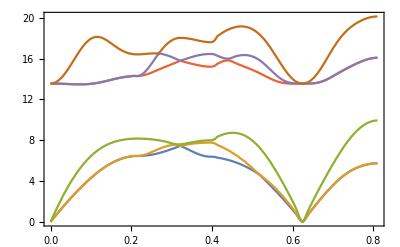

```mathematica
Plot[{interb[[1]][x],interb[[2]][x],interb[[3]][x],interb[[4]][x],interb[[5]][x],interb[[6]][x]},{x,0,0.81},Frame->True,Ticks->{{{0,"Γ"},{0.2,"X"},{0.32,"W"},{0.39,"K"},{0.62,"Γ"},{0.83,"L"}},{0,5,10,15,20}}]
```

```mathematica
With[{height=100,width=100,baseWidth=0.01},Table[(baseWidth+height*(interlw10[[i]][x]))*PDF[CauchyDistribution[interb[[i]][x],(baseWidth+width*(interlw10[[i]][x]))],y],{i,1,6}]];
pltB1l=Show[{DensityPlot[Total@%,{x,0,0.81},{y,-0.1,22},PlotRange->All,Frame->True,FrameStyle->Directive[Thickness[0.005]],FrameTicksStyle->Directive[20,Black],PlotPoints->100,FrameTicks->{{{0,5,10,15,20},None},{{{0,"Γ"},{0.2,"X"},{0.32,"W"},{0.39,"K"},{0.62,"Γ"},{0.81,"L"}},None}},FrameLabel->{Style["q (1/Å)",20,Black],Style["Energy (THz)",20,Black]},ColorFunction->GrayLevel,PlotTheme->"Scientific",PlotLabel->Style["10K",20,Black],PlotLegends->BarLegend[Automatic,Method->{FrameStyle->Directive[Thickness[0.005]],TicksStyle->Directive[FontSize->18,Black,AbsoluteThickness[2]]},LegendMarkerSize->250,LegendLabel->Style["2Γ(ω,StyleBox[\"T\",\nFontSlant->\"Italic\"])\n(10GHz)",18,Black]]],Plot[{interb[[1]][x],interb[[2]][x],interb[[3]][x],interb[[4]][x],interb[[5]][x],interb[[6]][x]},{x,0,0.81},PlotStyle->Directive[Orange,Opacity[0.25],Thickness[0.001]],PlotTheme->"Scientific"],Graphics[{Directive[{Orange,Dashed}],Line[{{0.202,0},{0.202,22}}]}],Graphics[{Directive[{Orange,Dashed}],Line[{{0.321,0},{0.321,22}}]}],Graphics[{Directive[{Orange,Dashed}],Line[{{0.397,0},{0.397,22}}]}],Graphics[{Directive[{Orange,Dashed}],Line[{{0.624,0},{0.624,22}}]}]},ImageSize->300]
```

-Graphics-

```mathematica
With[{height=10,width=10,baseWidth=0.01},Table[(baseWidth+height*(interlw300[[i]][x]))*PDF[CauchyDistribution[interb[[i]][x],(baseWidth+width*(interlw300[[i]][x]))],y],{i,1,6}]];
pltB2l=Show[{DensityPlot[Total@%,{x,0,0.81},{y,-0.1,22},PlotRange->All,Frame->True,FrameStyle->Directive[Thickness[0.005]],FrameTicksStyle->Directive[20,Black],PlotPoints->100,FrameTicks->{{{0,5,10,15,20},None},{{{0,"Γ"},{0.2,"X"},{0.32,"W"},{0.39,"K"},{0.62,"Γ"},{0.81,"L"}},None}},FrameLabel->{Style["q (1/Å)",20,Black],Style["Energy (THz)",20,Black]},ColorFunction->GrayLevel,PlotTheme->"Scientific",PlotLabel->Style["300K",20,Black],PlotLegends->BarLegend[Automatic,Method->{FrameStyle->Directive[Thickness[0.005]],TicksStyle->Directive[FontSize->18,Black,AbsoluteThickness[2]]},LegendMarkerSize->250,LegendLabel->Style["2Γ(ω,StyleBox[\"T\",\nFontSlant->\"Italic\"])\n(100GHz)",18,Black]]],Plot[{interb[[1]][x],interb[[2]][x],interb[[3]][x],interb[[4]][x],interb[[5]][x],interb[[6]][x]},{x,0,0.81},PlotStyle->Directive[Orange,Opacity[0.25],Thickness[0.001]],PlotTheme->"Scientific"],Graphics[{Directive[{Orange,Dashed}],Line[{{0.202,0},{0.202,22}}]}],Graphics[{Directive[{Orange,Dashed}],Line[{{0.321,0},{0.321,22}}]}],Graphics[{Directive[{Orange,Dashed}],Line[{{0.397,0},{0.397,22}}]}],Graphics[{Directive[{Orange,Dashed}],Line[{{0.624,0},{0.624,22}}]}]},ImageSize->300]
```

-Graphics-

```mathematica
With[{height=10,width=10,baseWidth=0.01},Table[(baseWidth+height*(interlw300[[i]][x]))*PDF[CauchyDistribution[interb[[i]][x],(baseWidth+width*(interlw300[[i]][x]))],y],{i,1,6}]];
pltB2l=Show[{DensityPlot[Total@%,{x,0,0.81},{y,-0.1,22},PlotRange->All,Frame->True,FrameTicksStyle->Directive[20,Black],PlotPoints->100,FrameLabel->{Style["Reciprocal space (Å^-1)",20,Black],Style["Energy (THz)",20,Black]},ColorFunction->GrayLevel,PlotTheme->"Scientific",PlotLabel->Style["300K",20,Black],PlotLegends->BarLegend[Automatic,Method->{TicksStyle->Directive[FontSize->18,Black,AbsoluteThickness[2]]},LegendMarkerSize->250,LegendLabel->Style["2Γ(ω,
StyleBox[\"T\",\nFontSlant->\"Italic\"])\n(100GHz)",18,Black]]],Plot[{interb[[1]][x],interb[[2]][x],interb[[3]][x],interb[[4]][x],interb[[5]][x],interb[[6]][x]},{x,0,0.81},PlotStyle->Directive[Orange,Opacity[0.9],Thickness[0.003]],PlotTheme->"Scientific"],
Graphics[{Text[Style["Γ",20,Bold,FontFamily->"Times",Hue[0.13]],{0.022,21}]}],Graphics[{Text[Style["X",20,Bold,FontFamily->"Times",Hue[0.13]],{0.232,21}]}],Graphics[{Text[Style["W",20,Bold,FontFamily->"Times",Hue[0.13]],{0.357,21}]}],Graphics[{Text[Style["K",20,Bold,FontFamily->"Times",Hue[0.13]],{0.427,21}]}],Graphics[{Text[Style["Γ",20,Bold,FontFamily->"Times",Hue[0.13]],{0.652,21}]}],
Graphics[{Text[Style["L",20,Bold,FontFamily->"Times",Hue[0.13]],{0.78,21}]}],Graphics[{Directive[{Orange,Dashed}],Line[{{0.202,0},{0.202,22}}]}],Graphics[{Directive[{Orange,Dashed}],Line[{{0.321,0},{0.321,22}}]}],Graphics[{Directive[{Orange,Dashed}],Line[{{0.397,0},{0.397,22}}]}],Graphics[{Directive[{Orange,Dashed}],Line[{{0.624,0},{0.624,22}}]}]},ImageSize->300]
```

-Graphics-

1000K

```mathematica
With[{height=5,width=5,baseWidth=0.01},Table[(baseWidth+height*(interlw1000[[i]][x]))*PDF[CauchyDistribution[interb[[i]][x],(baseWidth+width*(interlw1000[[i]][x]))],y],{i,1,6}]];
pltB3l=Show[{DensityPlot[Total@%,{x,0,0.81},{y,-0.1,22},PlotRange->All,Frame->True,FrameTicksStyle->Directive[20,Black],PlotPoints->100,FrameLabel->{Style["Reciprocal space (Å^-1)",20,Black],Style["Energy (THz)",20,Black]},ColorFunction->GrayLevel,PlotTheme->"Scientific",PlotLabel->Style["1000K",20,Black],PlotLegends->BarLegend[Automatic,Method->{TicksStyle->Directive[FontSize->18,Black,AbsoluteThickness[2]]},LegendMarkerSize->250,LegendLabel->Style["2Γ(ω,T)\n(200GHz)",18,Black]]],Plot[{interb[[1]][x],interb[[2]][x],interb[[3]][x],interb[[4]][x],interb[[5]][x],interb[[6]][x]},{x,0,0.81},PlotStyle->Directive[Orange,Opacity[0.9],Thickness[0.003]],PlotTheme->"Scientific"],
Graphics[{Text[Style["Γ",20,Bold,FontFamily->"Times",Hue[0.13]],{0.022,21}]}],Graphics[{Text[Style["X",20,Bold,FontFamily->"Times",Hue[0.13]],{0.232,21}]}],Graphics[{Text[Style["W",20,Bold,FontFamily->"Times",Hue[0.13]],{0.357,21}]}],Graphics[{Text[Style["K",20,Bold,FontFamily->"Times",Hue[0.13]],{0.427,21}]}],Graphics[{Text[Style["Γ",20,Bold,FontFamily->"Times",Hue[0.13]],{0.652,21}]}],
Graphics[{Text[Style["L",20,Bold,FontFamily->"Times",Hue[0.13]],{0.78,21}]}],Graphics[{Directive[{Orange,Dashed}],Line[{{0.202,0},{0.202,22}}]}],Graphics[{Directive[{Orange,Dashed}],Line[{{0.321,0},{0.321,22}}]}],Graphics[{Directive[{Orange,Dashed}],Line[{{0.397,0},{0.397,22}}]}],Graphics[{Directive[{Orange,Dashed}],Line[{{0.624,0},{0.624,22}}]}]},ImageSize->300]
```

-Graphics-

```mathematica
With[{height=1,width=1,baseWidth=0.01},Table[(baseWidth+height*(interlw3800[[i]][x]))*PDF[CauchyDistribution[interb[[i]][x],(baseWidth+width*(interlw3800[[i]][x]))],y],{i,1,6}]];
pltB4l=Show[{DensityPlot[Total@%,{x,0,0.81},{y,-0.1,22},PlotRange->All,Frame->True,FrameStyle->Directive[Thickness[0.005]],FrameTicksStyle->Directive[20,Black],PlotPoints->100,FrameTicks->{{{0,5,10,15,20},None},{{{0,"Γ"},{0.2,"X"},{0.32,"W"},{0.39,"K"},{0.62,"Γ"},{0.81,"L"}},None}},FrameLabel->{Style["q (1/Å)",20,Black],Style["Energy (THz)",20,Black]},ColorFunction->GrayLevel,PlotTheme->"Scientific",PlotLabel->Style["3800K",20,Black],PlotLegends->BarLegend[Automatic,Method->{FrameStyle->Directive[Thickness[0.005]],TicksStyle->Directive[FontSize->18,Black,AbsoluteThickness[2]]},LegendMarkerSize->250,LegendLabel->Style["2Γ(ω,StyleBox[\"T\",\nFontSlant->\"Italic\"])\n(THz)",18,Black]]],Plot[{interb[[1]][x],interb[[2]][x],interb[[3]][x],interb[[4]][x],interb[[5]][x],interb[[6]][x]},{x,0,0.81},PlotStyle->Directive[Orange,Opacity[0.25],Thickness[0.001]],PlotTheme->"Scientific"],Graphics[{Directive[{Orange,Dashed}],Line[{{0.202,0},{0.202,22}}]}],Graphics[{Directive[{Orange,Dashed}],Line[{{0.321,0},{0.321,22}}]}],Graphics[{Directive[{Orange,Dashed}],Line[{{0.397,0},{0.397,22}}]}],Graphics[{Directive[{Orange,Dashed}],Line[{{0.624,0},{0.624,22}}]}]},ImageSize->300]
```

-Graphics-

```mathematica
GraphicsGrid[{{pltB1l,pltB2l},{pltB3l,pltB4l}},ImageSize->800]
```

-Graphics-

```mathematica
Plot[Evaluate@Table[PDF[CauchyDistribution[25,i],y],{i,1,10}],{y,-30,50},PlotRange->All]
```

-Graphics-